### Generate plots of melting points vs. Z for various interesting ranges of elements

```mathematica
<<peeters`

peeters`setGitDir[ "../project/figures/phy487-qmsolids" ]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

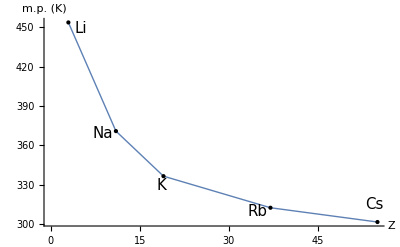

```mathematica
Clear[e, alkaliMetals, nobleGases, boronAndCarbon, oxygenAndNitrogen, transitionMetals4, transitionMetals5,transitionMetals6,meltPlot, period1, celcius] 

alkaliMetals = {3, 11, 19, 37, 55(*, 87*)} ;
nobleGases = { (*2,*) 10, 18, 36, 54, 86 } ;
period1 = Range[ 5, 8 ] ;
boronAndCarbon = { 5, 6 } ;
oxygenAndNitrogen  = { 7, 8 } ;
transitionMetals4 = Range[ 21, 30] ;
transitionMetals5 = Range[ 39, 48 ] ;
(*transitionMetals6 = Flatten[ {57, Range[ 72, 79 ] }] ;*)
transitionMetals6 = Range[ 57, 80 ]  ;

(********************************************************)
(* how-to-position-text-labels-automatically-to-not-overlap-other-graphics-elements/33064?noredirect=1#33064 *)
Clear[positionlabel, addlabels] ;
positionlabel[g_Graphics,{label_,x_}]:=Module[{p,b,bd,xi,m,ivp,sc},p=PlotRange[g];
b=ImagePad[ImagePad[Binarize@Show[g,ImagePadding->0],-1],1,Black];
bd=ImageDimensions[b];
xi=bd MapThread[Rescale,{x,p}];
m=MinFilter[b,1+Reverse[Rasterize[TraditionalForm@label,"RasterSize"]/2]];
ivp=ImageValuePositions[m,1];
sc=If[ivp=={},x,Scaled[First[Nearest[ivp,xi]]/bd]];
Graphics@Inset[label,sc,Center]]

addlabels[g_Graphics,labels_]:=Fold[Show[#1,positionlabel[##]]&,g,labels]

(*The labels must be supplied as a list like {{"label1",{x1,y1}},{"label2",{x2,y2}},...}.Here's an example:g=Plot[Sin[x],{x,0,10},Frame->True,Epilog->{PointSize[Large],Point[{#,Sin[#]}&/@Range[0,10]]}];

labels={Style[#,20],{#,Sin[#]}}&/@Range[0,10];

addlabels[g,labels]*)
(********************************************************)




(*meltPlot[e_] := Module[{meltingPoints, symbols},
meltingPoints = Map[ {{#, ElementData[#,"MeltingPoint"] + 273.2  }}&,e] ;
symbols = Map[ ElementData[#, "Symbol"] &,e] ;

ListPlot[ meltingPoints, PlotMarkers->  symbols, AxesLabel->{"Z", "m.p. (K)"} (*, PlotRange -> All*)]
] ;*)
(*Map[meltPlot[#] &, {alkaliMetals, nobleGases, boronAndCarbon, oxygenAndNitrogen(*, transitionMetals*)} ] *)

celcius := Quantity[#,"DegreesCelsius"] &;
meltPlot[e_] := Module[{meltingPoints, symbols, g},

(*meltingPoints: {{3,Quantity[453.74, "DegreesCelsius"]},{11,Quantity[370.91999999999996, "DegreesCelsius"]},{19,Quantity[336.58, "DegreesCelsius"]},{37,Quantity[312.51, "DegreesCelsius"]},{55,Quantity[301.64, "DegreesCelsius"]}}*)
meltingPoints = Map[ {#, First[ ElementData[#,"MeltingPoint"]] + 273.2  }&,e] ;

(*symbols: {{"Li",{3,Quantity[453.74, "DegreesCelsius"]}},{"Na",{11,Quantity[370.91999999999996, "DegreesCelsius"]}},{"K",{19,Quantity[336.58, "DegreesCelsius"]}},{"Rb",{37,Quantity[312.51, "DegreesCelsius"]}},{"Cs",{55,Quantity[301.64, "DegreesCelsius"]}}}*)
symbols = Map[ {Style[ElementData[#, "Symbol"], 15], {#, First[ElementData[#,"MeltingPoint"]] + 273.2  }} &,e] ;

(*why a second evaluation?*)
(*meltingPoints?]: {{3,Quantity[453.74, "DegreesCelsius"]},{11,Quantity[370.91999999999996, "DegreesCelsius"]},{19,Quantity[336.58, "DegreesCelsius"]},{37,Quantity[312.51, "DegreesCelsius"]},{55,Quantity[301.64, "DegreesCelsius"]}}*)
meltingPoints = Flatten[{#[[2]]} &/@ symbols, 1] ;

g= ListLinePlot[ meltingPoints
, AxesLabel->{"Z" // fs, "m.p. (K)" //fs}
(*, Frame->True*)
, PlotStyle-> Thick
,Epilog->{PointSize[Large],Point[# ]&/@meltingPoints}] ;

addlabels[g,symbols]

] 
meltPlot[ alkaliMetals ] 
(*meltPlot[ nobleGases ]
meltPlot[ boronAndCarbon ]
meltPlot[ oxygenAndNitrogen ]
meltPlot[ period1 ]
meltPlot[ transitionMetals4 ]
meltPlot[ transitionMetals5 ]
meltPlot[ transitionMetals6 ]*)

(*ElementData[3,"MeltingPoint"] // FullForm*)
```

```mathematica
(*SetDirectory[ "C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit" ] ;*)
Clear[plots, names]
plots ={meltPlot[ alkaliMetals ] ,
meltPlot[ nobleGases ],
meltPlot[ boronAndCarbon ],
meltPlot[ oxygenAndNitrogen ],
meltPlot[ period1 ],
meltPlot[ transitionMetals4 ],
meltPlot[ transitionMetals5 ],
meltPlot[ transitionMetals6 ]} ;
names = { "meltingPointsAlkaliMetalsFig1",
"meltingPointsNobleGasesFig2","meltingPointsBoronAndCarbonFig2","meltingPointsOxygenAndNitrogenFig3","meltingPointsPeriod1Fig4","meltingPointsTransitionMetalsPeriod4Fig5","meltingPointsTransitionMetalsPeriod5Fig6","meltingPointsTransitionMetalsPeriod6Fig7" } ;
(*plots*)
```

```mathematica
(*For[ i = 1, i ≤ 8, i++, Export[ names[[i]], plots[[i] ]] ]*)
Map[ peeters`exportForLatex[ names[[#]], plots[[#]]] &, Range[8] ]
```

{{meltingPointsAlkaliMetalsFig1.eps,meltingPointsAlkaliMetalsFig1pn.png},{meltingPointsNobleGasesFig2.eps,meltingPointsNobleGasesFig2pn.png},{meltingPointsBoronAndCarbonFig2.eps,meltingPointsBoronAndCarbonFig2pn.png},{meltingPointsOxygenAndNitrogenFig3.eps,meltingPointsOxygenAndNitrogenFig3pn.png},{meltingPointsPeriod1Fig4.eps,meltingPointsPeriod1Fig4pn.png},{meltingPointsTransitionMetalsPeriod4Fig5.eps,meltingPointsTransitionMetalsPeriod4Fig5pn.png},{meltingPointsTransitionMetalsPeriod5Fig6.eps,meltingPointsTransitionMetalsPeriod5Fig6pn.png},{meltingPointsTransitionMetalsPeriod6Fig7.eps,meltingPointsTransitionMetalsPeriod6Fig7pn.png}}